```mathematica
Monitor[Table[allGraphs4[k,"generators"]=FlatGenerators[allGraphs4[k,"colofour"]],{k,Sort[Keys[allGraphs4]]}],k];
```

```mathematica
FullBaseCoeff4[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs4[#,"colofour"]&,allGraphs4AtomKeys]}],CompareSymbols]}]
```

```mathematica
Sort[Table[var,{var,Map[allGraphs4[#,"colofour"]&,allGraphs4AtomKeys]}],CompareSymbols]
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}

```mathematica
EmptyBaseCoeff4[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs4[#,"colofourrealnull"]&,allGraphs4NullAtomKeys]}],CompareSymbols]}]
```

```mathematica
FullBaseCoeff4[allGraphs4[0,"colofour"]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
theGens4=Sort[Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&&Length[ListofVars[allGraphs4[#,"generators"]]]==1&],CompareSymbols[First[allGraphs4[#1,"generators"]],First[allGraphs4[#2,"generators"]]]&];
```

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"v"->prefix]]
```

```mathematica
repGen4=First[Solve[Table[ChangeSymbol[First[allGraphs4[k,"generators"]],"g"]==allGraphs4[k,"colofour"],{k,theGens4}],Table[allGraphs4[m,"colofour"],{m,allGraphs4AtomKeys}]]];
```

```mathematica
Monitor[Table[allGraphs4[k,"genfour"]=Simplify[allGraphs4[k,"colofour"]/.repGen4],{k,Sort[Keys[allGraphs4]]}],k];
```

```mathematica
DocValue4[key_]:=With[
{rep=Join[
Table[ChangeSymbol[k,"g"]->Style[ChangeSymbol[k,"g"],Red,Bold],{k,FlatGenerators[allGraphs4[key,"generators"]]}],
Table[k->Style[k,Red],{k,FlatGenerators[allGraphs4[key,"generators"]]}]]},
Table[allGraphs4[key,code]/.rep,{code,{"generators","genfour","colofour"}}]
]
```

```mathematica
GenIndices4[key_]:=Block[{gens=Map[ChangeSymbol[#,"g"]&,FlatGenerators[allGraphs4[key,"generators"]]],gens2=Map[ChangeSymbol[#,"v"]&,FlatGenerators[allGraphs4[key,"generators"]]],genForm=allGraphs4[key,"genfour"],
genColor=allGraphs4[key,"colofour"]},
With[{a=Table[Coefficient[genForm,var],{var,gens}],b=Table[Coefficient[genColor,var],{var,gens2}]},
{
a,
b,
a==b
}
]
]
```

```mathematica
MobGen[k_]:=With[{
m=MobiusGraph4[K4Key,allGraphs4],
gen=Map[ChangeSymbol[#,"n"]&,allGraphs4[k,"generators"]],
full=Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs4[k,"colofour"]]]
},
Graph[VertexList[m],EdgeList[m],VertexStyle->Table[v->Blue,{v,gen}],VertexLabels->Table[v->SymbolName[v],{v,full}]]
]
```

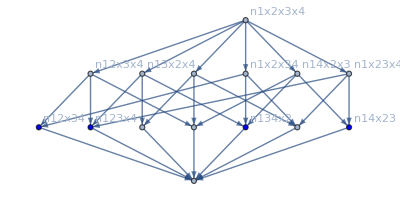

```mathematica
MobGen[3]
```

```mathematica
ChangeSymbolEmpty[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"g"->prefix]]
```

```mathematica
ChangeSymbolEmpty2[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"n"->prefix]]
```

```mathematica
MobGen2[k_]:=With[{
m=MobiusGraph4[K4Key,allGraphs4],
gen=Sort[Map[ChangeSymbolEmpty[#,"n"]&,ListofVars[allGraphs4[k,"genfour"]]],CompareSymbols],
full=Sort[Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs4[k,"colofour"]]],CompareSymbols]
},
Labeled[
Graph[VertexList[m],EdgeList[m],VertexStyle->Table[v->Blue,{v,gen}],VertexLabels->Table[v->Column[{SymbolName[v],Coefficient[allGraphs4[k,"genfour"],ChangeSymbolEmpty2[v,"g"]]}],{v,full}]],
ToString[gen]==ToString[full]
]
]
```

```mathematica
Coefficient[allGraphs4[1,"genfour"],ChangeSymbol[g12x3x4,"g"]]
```

-1

```mathematica
allGraphs4[0,"genfour"]
```

g1234

```mathematica
GenIndices4[271]
```

{{1,1},{1,1},True}

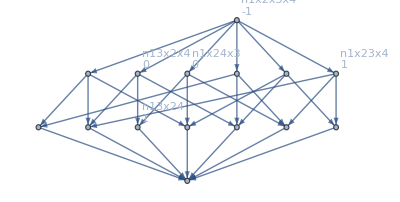
-Graphics-False{g13x24+g1x23x4-g1x2x3x4,v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4}

```mathematica
Labeled[MobGen2[271],{allGraphs4[271,"genfour"],allGraphs4[271,"colofour"]}]
```

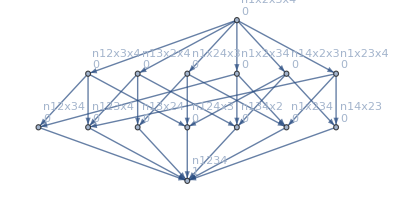
-Graphics-False

```mathematica
MobGen2[0]
```

```mathematica
XPower[sym_]:=x^(1+StringCount[SymbolName[sym],"x"])
```

```mathematica
genRep4=Table[allGraphs4[k,"genfour"]->ChromaticPolynomial[allGraphs4[k,"graph"],x],{k,theGens4}]
```

{g1x2x3x4→-6 x+11 x^2-6 x^3+x^4,g1x2x34→-4 x+8 x^2-5 x^3+x^4,g1x23x4→-4 x+8 x^2-5 x^3+x^4,g1x24x3→-4 x+8 x^2-5 x^3+x^4,g12x3x4→-4 x+8 x^2-5 x^3+x^4,g13x2x4→-4 x+8 x^2-5 x^3+x^4,g14x2x3→-4 x+8 x^2-5 x^3+x^4,g12x34→-3 x+6 x^2-4 x^3+x^4,g13x24→-3 x+6 x^2-4 x^3+x^4,g14x23→-3 x+6 x^2-4 x^3+x^4,g1x234→-x+3 x^2-3 x^3+x^4,g123x4→-x+3 x^2-3 x^3+x^4,g124x3→-x+3 x^2-3 x^3+x^4,g134x2→-x+3 x^2-3 x^3+x^4,g1234→x^4}

```mathematica
Table[CoefficientList[ChromaticPolynomial[allGraphs4[k,"graph"],x],x],{k,theGens4}]//MatrixForm
```

(0 | -6 | 11 | -6 | 1
0 | -4 | 8 | -5 | 1
0 | -4 | 8 | -5 | 1
0 | -4 | 8 | -5 | 1
0 | -4 | 8 | -5 | 1
0 | -4 | 8 | -5 | 1
0 | -4 | 8 | -5 | 1
0 | -3 | 6 | -4 | 1
0 | -3 | 6 | -4 | 1
0 | -3 | 6 | -4 | 1
0 | -1 | 3 | -3 | 1
0 | -1 | 3 | -3 | 1
0 | -1 | 3 | -3 | 1
0 | -1 | 3 | -3 | 1
0 | 0 | 0 | 0 | 1)

```mathematica
fullRep4=Table[allGraphs4[k,"colofour"]->ChromaticPolynomial[allGraphs4[k,"graph"],x],{k,allGraphs4AtomKeys}]
```

{v1x2x3x4→-6 x+11 x^2-6 x^3+x^4,v1x2x34→2 x-3 x^2+x^3,v1x24x3→2 x-3 x^2+x^3,v1x23x4→2 x-3 x^2+x^3,v1x234→-x+x^2,v14x2x3→2 x-3 x^2+x^3,v14x23→-x+x^2,v13x2x4→2 x-3 x^2+x^3,v13x24→-x+x^2,v134x2→-x+x^2,v12x3x4→2 x-3 x^2+x^3,v12x34→-x+x^2,v124x3→-x+x^2,v123x4→-x+x^2,v1234→x}

```mathematica
MobGen3[k_]:=With[{
m=MobiusGraph4[K4Key,allGraphs4],
gen=allGraphs4[k,"genfour"],
full=allGraphs4[k,"colofour"]
},
Simplify[{ChromaticPolynomial[allGraphs4[k,"graph"],x], gen,full,(gen/.genRep4),(full/.fullRep4)}]
]
```

```mathematica
MobGen3[1]
```

{(-1+x) x^3,g123x4+g124x3-g12x3x4+g13x24-g13x2x4+g14x23-g14x2x3-g1x23x4-g1x24x3+2 g1x2x3x4,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4,(-1+x) x^3,(-1+x) x^3}

```mathematica
Table[ShowGraph[allGraphs4,k]->GenIndices4[k],{k,Take[Keys[allGraphs4],20]}]
```

{-Graphics-0→{{1},{1},True},-Graphics-243→{{1,1,1,1},{1,1,1,1},True},-Graphics-324→{{1,1},{1,1},True},-Graphics-351→{{1},{1},True},-Graphics-360→{{1,1},{1,1},True},-Graphics-363→{{1},{1},True},-Graphics-364→{{1},{1},True},-Graphics-365→{{1},{1},True},-Graphics-367→{{1},{1},True},-Graphics-361→{{1},{1},True},-Graphics-369→{{1},{1},True},-Graphics-373→{{1},{1},True},-Graphics-377→{{1},{1},True},-Graphics-354→{{1,1},{1,1},True},-Graphics-355→{{1},{1},True},-Graphics-357→{{1},{1},True},-Graphics-352→{{1,1},{1,1},True},-Graphics-353→{{1},{1},True},-Graphics-382→{{1},{1},True},-Graphics-391→{{1},{1},True}}

```mathematica
Table[ShowGraph[allGraphs4,k]->DocValue4[k],{k,Take[Keys[allGraphs4],10]}]
```

{-Graphics-0→{{v1234},g1234,v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4+v1234},-Graphics-243→{{v1x234,v14x23,v13x24,v134x2},-g13x2x4-g14x2x3-g1x23x4-g1x24x3-g1x2x34+2 g1x2x3x4+g134x2+g13x24+g14x23+g1x234,v13x2x4+v14x2x3+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4+v134x2+v13x24+v14x23+v1x234},-Graphics-324→{{v1x234,v14x23},-g1x23x4+g14x23+g1x234,v14x2x3+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4+v14x23+v1x234},-Graphics-351→{{v1x234},g1x234,v1x23x4+v1x24x3+v1x2x34+v1x2x3x4+v1x234},-Graphics-360→{{v1x2x34,v1x24x3},-g1x2x3x4+g1x24x3+g1x2x34,v1x2x3x4+v1x24x3+v1x2x34},-Graphics-363→{{v1x2x34},g1x2x34,v1x2x3x4+v1x2x34},-Graphics-364→{{v1x2x3x4},g1x2x3x4,v1x2x3x4},-Graphics-365→{{v1x2x34},-g1x2x3x4+g1x2x34,v1x2x34},-Graphics-367→{{v1x24x3},-g1x2x3x4+g1x24x3,v1x24x3},-Graphics-361→{{v1x24x3},g1x24x3,v1x2x3x4+v1x24x3}}

```mathematica
GenBaseCoeff[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Table[ChangeSymbol[First[allGraphs4[k,"generators"]],"g"],{k,theGens4}]}],CompareSymbols]}]
```

```mathematica
Table[With[{c=EmptyBaseCoeff4[allGraphs4[k,"colofourrealnull"]]},{Min[c],Max[c]}],{k,theGens4}]//Tally
```

{{{-6,2},1},{{-4,2},6},{{-3,1},3},{{-1,1},4},{{0,1},1}}

```mathematica
{{{-120,24},1},{{-94,24},15},{{-78,18},45},{{-54,18},20},{{-44,14},15},{{-44,14},40},{{-14,8},15},{{-31,7},10},{{-15,7},15},{{-1,1},4},{{0,1},1}}
```

{{{-120,24},1},{{-94,24},15},{{-78,18},45},{{-54,18},20},{{-44,14},15},{{-44,14},40},{{-14,8},15},{{-31,7},10},{{-15,7},15},{{-1,1},4},{{0,1},1}}

```mathematica
EmptyBaseCoeff4[allGraphs4[1,"colofourrealnull"]]
```

{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
theGens4Comp=Table[FindComplement[k,allGraphs4],{k,theGens4}]
```

{0,1,9,3,243,81,27,244,84,36,13,333,273,109,364}

```mathematica
SummarizeGenerators[k_]:=Block[{gen=BaseGenerators[allGraphs4[k,"colofour"]],keys},
keys=Keys[gen];
Table[{kk,Length[gen[kk]]},{kk,Sort[keys]}]]
```

```mathematica
SummarizeGenerators[1]
```

{{2,4}}

```mathematica
Table[SummarizeGenerators[k],{k,theGens4Comp}]
```

{{{1,1}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,2}},{{2,2}},{{2,2}},{{3,3}},{{3,3}},{{3,3}},{{3,3}},{{4,1}}}

```mathematica
Multicolumn[Table[Framed[Labeled[{
ShowGraph[allGraphs4,k],
ShowGraph[allGraphs4,FindComplement[k,allGraphs4]]
},SymbolToLabel2[allGraphs4[k,"generators"]//First,4],Top]],{k,theGens4}],8,Appearance->"Horizontal"]
```

{-Graphics-364,-Graphics-0}OverHat[1] | {-Graphics-363,-Graphics-1}34 | {-Graphics-355,-Graphics-9}23 | {-Graphics-361,-Graphics-3}24 | {-Graphics-121,-Graphics-243}12 | {-Graphics-283,-Graphics-81}13 | {-Graphics-337,-Graphics-27}14 | {-Graphics-120,-Graphics-244}12♁34
{-Graphics-280,-Graphics-84}13♁24 | {-Graphics-328,-Graphics-36}14♁23 | {-Graphics-351,-Graphics-13}234 | {-Graphics-31,-Graphics-333}123 | {-Graphics-91,-Graphics-273}124 | {-Graphics-255,-Graphics-109}134 | {-Graphics-0,-Graphics-364}OverHat[0] |

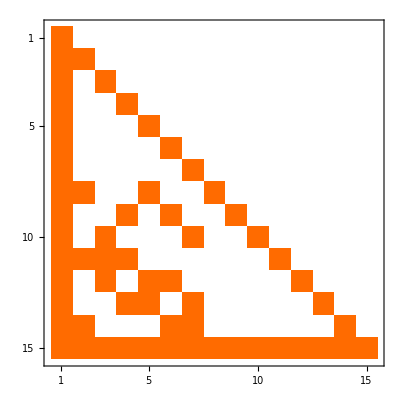

```mathematica
mat=Table[
FullBaseCoeff4[allGraphs4[k,"colofour"]],
{k,theGens4}
];MatrixPlot[mat]
```

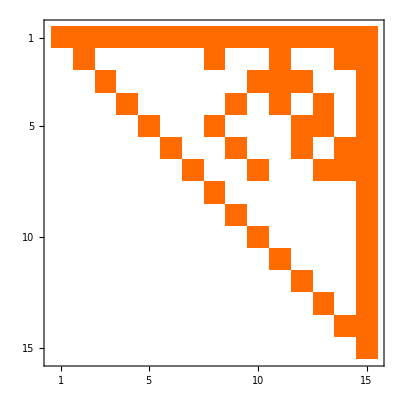

```mathematica
mat2=Table[
FullBaseCoeff4[allGraphs4[k,"colofour"]],
{k,Sort[allGraphs4NullAtomKeys,CompareSymbols[allGraphs4[#1,"colofourrealnull"],allGraphs4[#2,"colofourrealnull"]]&]}
];MatrixPlot[mat2]
```

```mathematica
mat==Transpose[mat2]
```

True

## Mobius and zeta

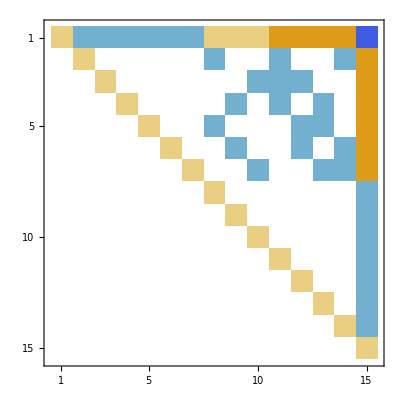

```mathematica
mob4=MobiusMatrix[allGraphs4];MatrixPlot[mob4]
```

```mathematica
zeta4=Inverse[mob4];MatrixPlot[zeta4]
```

-Graphics-

```mathematica
zeta4Transp=Transpose[zeta4];MatrixPlot[zeta4Transp]
```

-Graphics-

```mathematica
Map[ShowGraph[allGraphs4,#]&,Table[
Select[Keys[allGraphs4],FullBaseCoeff4[allGraphs4[#,"colofour"]]==zeta4Transp[[k]]&]//First,
{k,1,15}
]]
```

{-Graphics-364,-Graphics-363,-Graphics-355,-Graphics-361,-Graphics-121,-Graphics-283,-Graphics-337,-Graphics-120,-Graphics-280,-Graphics-328,-Graphics-351,-Graphics-31,-Graphics-91,-Graphics-255,-Graphics-0}

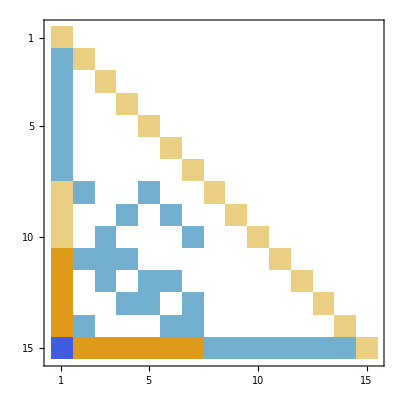

```mathematica
mob4Transp=Transpose[mob4];MatrixPlot[mob4Transp]
```

```mathematica
Table[
Select[Keys[allGraphs4],EmptyBaseCoeff4[allGraphs4[#,"colofourrealnull"]]==Reverse[mob4Transp[[k]]]&],
{k,1,15}
]
```

{{728},{473},{637},{697},{377},{400},{448},{},{},{},{},{},{},{},{}}

```mathematica
ShowGraph[allGraphs4,400]
```

-Graphics-400

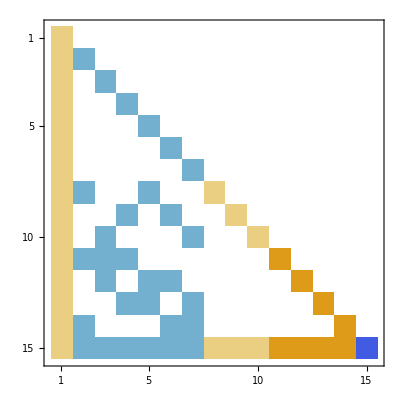

```mathematica
compSomthing=Table[EmptyBaseCoeff4[allGraphs4[k,"colofourrealnull"]],{k,Sort[Select[Keys[allGraphs4],Length[ListofVars[allGraphs4[#,"colofournull"]]]==1&],CompareSymbols[allGraphs4[#1,"colofournull"],allGraphs4[#2,"colofournull"]]&]}];MatrixPlot[compSomthing]
```

```mathematica
daig=Diagonal[(mob4Transp.compSomthing)]
```

{1,-1,-1,-1,-1,-1,-1,1,1,1,2,2,2,2,-6}

```mathematica
Diagonal[(compSomthing.mob4Transp)]
```

{1,-1,-1,-1,-1,-1,-1,1,1,1,2,2,2,2,-6}

```mathematica
compSomthing.daig
```

{1,2,2,2,2,2,2,4,4,4,8,8,8,8,62}